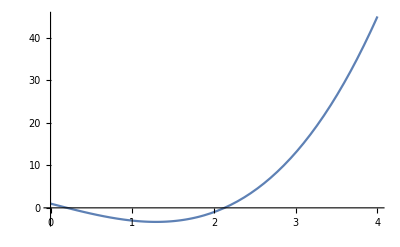

```mathematica
NewtonRE[x0_,error_,f_]:=
Module[{xk1,xk=N[x0]},
k=0;
Output={{k,x0,f[x0],None}};
approxE=10000000;
While[approxE>error,fPrimexk=f'[xk];
If[fPrimexk==0,Print["The derivation of function at ",k," th iteration is zero, we cannot proceed further with iterative scheme"];Break[];];
xk1=xk-f[xk]/fPrimexk;
approxE=Abs[xk1-xk];
xk=xk1;
k++;
Output=Append[Output,{k,xk,f[xk],approxE}];];
Print[NumberForm[TableForm[Output,
TableHeadings->{None,{"k","xk","f[xk]","Approx Error"}}],8]];
Print["Number of iterations required to achieve desired accuracy = ",k];
Print["Root after ",k," iterations xk= ",NumberForm[xk,8]];
Print["Function value at approximated root, f[xk]= ",NumberForm[f[xk],8]];];
f[x_]:=x^3-5x+1;
error=10^(-4);
Plot[f[x],{x,0,4}]
```

```mathematica
Question 1
```

```mathematica
NewtonRE[0.5,error,f]
```

k | xk | f[xk] | Approx Error
0 | 0.5 | -1.375 | None
1 | 0.17647059 | 0.12314268 | 0.32352941
2 | 0.20156807 | 0.0003492764 | 0.025097486
3 | 0.20163968 | 3.1004843×10^-9 | 0.000071600749

Number of iterations required to achieve desired accuracy = 3

Root after 3 iterations xk= 0.20163968

Function value at approximated root, f[xk]= 3.1004843×10^-9

```mathematica
Question 2
```

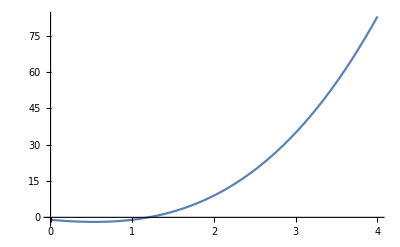

```mathematica
f[x_]:=x^3+2x^2-3x-1;
error=10^(-5);
Plot[f[x],{x,0,4}]
```

```mathematica
NewtonRE[2,error,f];
```

k | xk | f[xk] | Approx Error
0 | 2 | 9 | None
1 | 1.4705882 | 2.0938327 | 0.52941176
2 | 1.2471327 | 0.30899704 | 0.22345556
3 | 1.2006987 | 0.012278977 | 0.046433946
4 | 1.1986949 | 0.000022485706 | 0.002003806
5 | 1.1986912 | 7.5904616×10^-11 | 3.682928×10^-6

Number of iterations required to achieve desired accuracy = 5

Root after 5 iterations xk= 1.1986912

Function value at approximated root, f[xk]= 7.5904616×10^-11